## Initialization Notation

```mathematica
(*get association of resources,name of local host and remove local host from available resources*)
(*hosts=Counts[ReadList[Environment["NODEFILE"],"String"]]
local=First[StringSplit[Environment["HOSTNAME"],"."]]
hosts[local]--;
(*launch subkernels and connect them to the controlling Wolfram Kernel*)
Needs["SubKernels`RemoteKernels`"];
Map[If[hosts[#]>0,LaunchKernels[RemoteMachine[#,"ssh -x -f -l `3` `1` /gpfs/runtime/opt/mathematica/12.0/Executables/wolfram -wstp -linkmode Connect `4` -linkname '`2`' -subkernel -noinit",hosts[#]]]]&,Keys[hosts]];
dir=DirectoryName[$InputFileName];*)
```

```mathematica
Unprotect[Out];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
<<NDSolve`FEM`
dir=NotebookDirectory[];
SetDirectory[dir]
```

D:\Dropbox (Brown)\Apps\HyperElastic_Mathematica\Abaqus_Validation

```mathematica
ClearAll[PlotMeshBC]
Protect[ShowMesh,ShowNumbers,ShowBCs];
Options[PlotMeshBC]={ShowMesh->False,ShowNumbers->False,ShowBCs->False};
PlotMeshBC[DirichletPoints_,NeumannPoints_,OptionsPattern[]]:=
If[OptionValue[ShowMesh],
Block[{PltPoints,plt},
Switch[OptionValue[ShowBCs]
,"DirichletBC"
,PltPoints =Cases[DirichletPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,"NeumannBC"
,PltPoints =Cases[NeumannPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,False
,plt =False;];
Show[
Join[{mesh["Wireframe"]}
,
If[OptionValue[ShowNumbers]
,{mesh["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]]
,mesh["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]},{}]
,
If[plt
,Switch[ndof
,2,{Graphics[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]}
,3,{Graphics3D[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics3D[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]
,Graphics3D[{PointSize[Large],Purple,Opacity[0.3],Point[Coords[[PltPoints[[3]]]]]}]}
],{}]
]
,ViewPoint->{1.5,1,1}]
],Null];

PrintBB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Blue,Bold]&/@X)];
]
PrintRB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Red,Bold]&/@X)];
]
```

## Problem Solution: Numerics

### Boundary condition

```mathematica
ClearAll[DefineBCs,Edgedet];
DefineBCs[uVec_,tVec_,L_,r_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Lft,Bck,Rit,RitBttm,Tp,Nodes},
Bttm =Flatten@Position[Abs[Coords[[;;,3]]-0.0],x_/;x<tol];
Lft=Flatten@Position[Abs[Coords[[;;,2]]-(-r)],x_/;x<tol];
Bck=Flatten@Position[Abs[Coords[[;;,1]]-(-r)],x_/;x<tol];
(*Nodes = Join[{1,#}&/@Bck,{2,#}&/@Lft,{3,#}&/@Bttm]*)
Nodes = Join[{1,#}&/@Bttm,{2,#}&/@Bttm,{3,#}&/@Bttm]
(*Nodes = Join[{1,#}&/@Extract[Rit,RitBttm],{2,#}&/@Extract[Bttm,BttmRit],{2,#}&/@Tp]*)
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,Rit,Frnt,ETp,ERit,EFrnt,Nodes},
Tp=Flatten@Position[Abs[Coords[[;;,3]]-L],x_/;x<tol];
Rit=Flatten@Position[Abs[Coords[[;;,2]]-(r)],x_/;x<tol];
Frnt=Flatten@Position[Abs[Coords[[;;,1]]-(r)],x_/;x<tol];
ETp=Edgedet@{0,0,-1};
ERit=Edgedet@{0,-1,0};
EFrnt=Edgedet@{-1,0,0};
Edges=Join[{1,#}&/@EFrnt,{2,#}&/@ERit,{3,#}&/@ETp];
(*Nodes =  {3,#}&/@Tp*)
Nodes = Join[{1,#}&/@Frnt,{2,#}&/@Rit,{3,#}&/@Tp]
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
Edgedet[n_]:=Extract[mesh["BoundaryElements"][[1,1]],Position[Map[Norm@(#-n)&,mesh["BoundaryNormals"][[1]]],x_/;x<10^-5]];
```

### Apply Traction

```mathematica
ClearAll[ApplyTraction];
SetAttributes[ApplyTraction,HoldFirst];
ApplyTraction[rMat_,edge_]:=
Block[{
ElementType=Head@mesh["BoundaryElements"][[1]],
elementOrder=mesh["MeshOrder"],
integrationOrder,
ELEtMat=ConstantArray[0.0,{ndof,nsen}]
,OutEdge,coord,jacobi,ELEt,Q
,GuassPointsNatural,GuassWeights,NMat,dN,NetTrctn
},
integrationOrder=If[ElementType===QuadElement,2elementOrder,elementOrder];
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];
dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
(*OutEdge=Flatten[Outer[List,Range[ndof],Edge],1];*)
OutEdge={edge[[1]],#}&/@edge[[2]];
coord =Coords[[edge[[2]]]];
jacobi =If[ndof==3,Norm[Cross@@((dN@@#).coord)]&
,Norm[(dN@@#).coord]&];
ELEtMat=ReplacePart[ELEtMat,edge[[1]]->Map[NeumannBC,OutEdge]];
(*ELEtMat=ArrayReshape[ReplacePart[Map[NeumannBC,OutEdge],Position[KeyExistsQ[NeumannBC,#]&/@OutEdge,False]->0.0],{ndof,nsen}];*)
ELEt=jacobi[#](ELEtMat.NMat@@#)&;
NetTrctn=GuassWeights.(ELEt/@GuassPointsNatural);
Q=Flatten@IDMat[[;;,edge[[2]]]];
rMat[[Q]]+=Flatten[ConstantArray[#/nsen,nsen]&/@NetTrctn];
]
```

### Neo-Hookean Constitutive law

```mathematica
NeoHookenS[e0_,BMat:_,ELEu:_,ξ_List,typeId_]:=
Block[{e=e0
,F,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
F=ℐ+BMat[ξ].ELEu;
J=Det[F];
B=F.Transpose[F];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
(*σ= μ/J^(5/3)(B-TrB/3 ℐ)+Κ(J-1)ℐ;*)
σ=Switch[typeId,1,μ/J^(5/3)(B-TrB/3 ℐ),2,Κ(J-1)ℐ];
τ = J σ
]
NeoHookenC[e0_,BMat:_,ELEu:_,ξ_List,typeId_]:=
Block[{e=e0
,F,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
F=ℐ+BMat[ξ].ELEu;
J=Det[F];
B=F.Transpose[F];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
Switch[typeId,1
,μ/J^(2/3)(Transpose[ℐ⊗B,{1,3,2,4}]+Transpose[B⊗ℐ,{1,3,4,2}]
-2/3(B⊗ℐ+ℐ⊗B)+2/3 TrB/3 ℐ⊗ℐ)
,2,Κ(2J-1)J ℐ⊗ℐ]
]

StVenantS[e0_,BMat:_,ELEu:_,ξ_List,typeId_]:=
Block[{e=e0
,F,J,ΕL,TrΕL,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
F=ℐ+BMat[ξ].ELEu;
ΕL=1/2(Transpose[F].F-ℐ);
TrΕL = If[ndof==3,Tr[ΕL],Tr[ΕL]+1];(*difference in 3D and 2D*)
Switch[typeId,1,2 μ F.ΕL.Transpose[F],2,λ TrΕL  F.Transpose[F] ]
]
StVenantC[e0_,BMat:_,ELEu:_,ξ_List,typeId_]:=
Block[{e=e0
,F,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
F=ℐ+BMat[ξ].ELEu;
J=Det[F];
B=F.Transpose[F];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
Switch[typeId,1
,μ/J^(2/3)(Transpose[ℐ⊗B,{1,3,2,4}]+Transpose[B⊗ℐ,{1,3,4,2}]
-2/3(B⊗ℐ+ℐ⊗B)+2/3 TrB/3 ℐ⊗ℐ)
,2,Κ(2J-1)J ℐ⊗ℐ]
]
```

### Stiffness and Residual

```mathematica
ClearAll[DefineGaussAndSFInfo,GuassIntegrate];
Options[DefineGaussAndSFInfo]={ReducedIntegration->False};
DefineGaussAndSFInfo[ElementType_,elementOrder_,OptionsPattern[]]:=
Block[{integrationOrder=If[!OptionValue[ReducedIntegration]&&((ElementType===HexahedronElement)||(ElementType===QuadElement)),2elementOrder,elementOrder]},
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
(*GaussIndex=AssociationMap[Position[GuassPointsNatural,#][[1,1]]&,GuassPointsNatural];*)
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];
dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
];
GuassIntegrate[coord_List,f0_]:=
Block[{f=f0,GuassPointsSpatial},
GuassPointsSpatial=Apply[NMat,GuassPointsNatural,2].coord;
GuassWeights.MapThread[f,{GuassPointsNatural,GuassPointsSpatial}]
];
```

```mathematica
ClearAll[ComputeResidualMatrixU];
SetAttributes[ComputeResidualMatrixU,HoldFirst];
ComputeResidualMatrixU[rMat_,e0_,UMat_,dt_,ElTypId_,typeId_]:=
Block[{e=e0
,B,Q,jacobi,BMat,ELEf,ELEr,ELEd,ℐr,ELEu,coord,ELEσ,NBMat
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;(*ndof × nen*)
ELEu=Transpose[UMat[[;;,B]]]; (*nen × ndof*)
NBMat=Transpose[BMat[#]].Inverse[ℐ+BMat[#].ELEu]&;(*nen × ndof*)
ELEr=jacobi[#]*Kirchhoff[e,BMat,ELEu,#,typeId].Transpose[NBMat[#]]&;(*ndof × nen*)
(*ELEσ=TensorContract[Switch[typeId,1,StiffnessDev,2,StiffnessVol].(BMat[#].ELEu),{3,4}]&;(*ndof × ndof*)*)
(*ELEr=jacobi[#]*stress[e,dt,BMat,ELEu,ElTypId,#][[;;ndof,;;ndof]].BMat[#]&;*)
ELEd=(*ELEf[#1,#2]*)-ELEr[#1]&;
ℐr= Flatten@GuassIntegrate[coord,ELEd]; (*ndof ⊕ nen*)
rMat[[Q]]+=ℐr;
]

ClearAll[ComputeStiffnessMatrixU];
SetAttributes[ComputeStiffnessMatrixU,HoldFirst];
ComputeStiffnessMatrixU[KMat_,e0_,UMat_,dt_,ElTypId_,typeId_]:=
Block[{e=e0
,B,Q,jacobi,BMat,ELEk,ℐk,coord,ELEu,NBMat
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;(*ndof × nen*)
ELEu=Transpose[UMat[[;;,B]]]; (*nen × ndof*)
NBMat=Transpose[BMat[#]].Inverse[ℐ+BMat[#].ELEu]&; (*nen × ndof*)
ELEk=jacobi[#]*(TensorContract[NBMat[#]⊗Tangent[e,BMat,ELEu,#,typeId],{2,4}].Transpose[NBMat[#]]-Transpose[(Kirchhoff[e,BMat,ELEu,#,typeId].Transpose[NBMat[#]])⊗NBMat[#],{2,4,1,3}])&;
(*nen × ndof × ndof × nen*)
(*ELEk=jacobi[#]BMat[#]^ᵀ.Tangent[e,dt,BMat,ELEu,ElTypId,#].BMat[#]&;*)
(*ELEk=jacobi[#]BMat[#]^ᵀ.Switch[typeId,1,StiffnessDev,2,StiffnessVol].BMat[#]&;(*nen × ndof × ndof × nen*)*)
ℐk=Flatten[GuassIntegrate[coord,ELEk],{{2,1},{3,4}}];(*ndof ⊕ nen × ndof ⊕ nen*)
KMat[[Q,Q]]+=ℐk;
]
```

```mathematica
CalrMat[UMat_,dt_,ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,rMatVol,rMatDev
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[rMatDev=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMatDev,n,UMat,dt,ElTypId,1],{n,Range[nel[[ElTypId]]]}];
rMatDev=Plus@@(ParallelEvaluate@rMatDev);
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder,ReducedIntegration->True];
ParallelEvaluate[rMatVol=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMatVol,n,UMat,dt,ElTypId,2],{n,Range[nel[[ElTypId]]]}];
rMatVol=Plus@@(ParallelEvaluate@rMatVol);
rMatDev+rMatVol
];
CalKMat[UMat_,dt_,ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,KMatVol,KMatDev
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[KMatDev=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMatDev,n,UMat,dt,ElTypId,1],{n,Range[nel[[ElTypId]]]}];
KMatDev=Plus@@(ParallelEvaluate@KMatDev);
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder,ReducedIntegration->True];
ParallelEvaluate[KMatVol=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMatVol,n,UMat,dt,ElTypId,2],{n,Range[nel[[ElTypId]]]}];
KMatVol=Plus@@(ParallelEvaluate@KMatVol);
KMatDev+KMatVol
]

ParallelResidual[UMat_,dt_,TracInd_]:= 
Block[{rMat,Err,tMat},
rMat=Plus@@(CalrMat[UMat,dt,#]&/@Range@nElTyp);
If[TracInd,
ParallelEvaluate[tMat=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ApplyTraction[tMat,edge],{edge,Edges}];
tMat=Plus@@(ParallelEvaluate@tMat);
rMat+=tMat;
];
(*If[TracInd,ApplyTraction[rMat,#]&/@Edges;];*)
Err =Norm[rMat[[IDno]],Infinity];
{Err,rMat}
]

ParallelStiffness[UMat_,dt_]:= 
Block[{KMat},
KMat=Plus@@(CalKMat[UMat,dt,#]&/@Range@nElTyp);
KMat
]
```

### Post-processing subroutine

```mathematica
ClearAll[ComputeStressProjection];
SetAttributes[ComputeStressProjection,HoldFirst];
ComputeStressProjection[{aMat_,UdMat_},e0_,UMat_,(*σ_,*)ElTypId_]:=
Block[{e=e0,B,jacobi,BMat,ℐk,ℐf,ff,fk,coord,ELEu,ELEσ},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
fk=jacobi[#](NMat@@#)⊗(NMat@@#)&;
ℐk=GuassIntegrate[coord,fk];
aMat[[B,B]]+=ℐk;
ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;
ff=jacobi[#](NMat@@#)⊗Flatten[ELEσ[#]]&;
(*ff=jacobi[#](NMat@@#)⊗Flatten[σ[[e,GaussIndex@#]]]&;*)
ℐf=GuassIntegrate[coord,ff];
UdMat[[B,;;]]+=ℐf;
]

CalAUdMat[UMat_,(*σ_,*)ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,aMat,UdMat
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[aMat=SparseArray[{},{nnp,nnp},0.0]];
ParallelEvaluate[UdMat=ConstantArray[0.0,{nnp,nud}]];
ParallelDo[ComputeStressProjection[{aMat,UdMat},n,UMat,(*σ,*)ElTypId],{n,Range[nel[[ElTypId]]]}];
aMat=Plus@@(ParallelEvaluate@aMat);
UdMat=Plus@@(ParallelEvaluate@UdMat);
{aMat,UdMat}
]

StressRecover[UMat_(*,σ_*)]:=
Block[{
nud= ndof*ndof,AUdMat,aMat,UdMat,SolUd,SolUdMat,StressMat,StressMatf
},
AUdMat=CalAUdMat[UMat(*,σ[[#]]*),#]&/@(Range@nElTyp);
aMat=Plus@@AUdMat[[;;,1]];
UdMat=Plus@@AUdMat[[;;,2]];
SolUd=LinearSolve[aMat,UdMat];
StressMat=ArrayReshape[SolUd,{Length@SolUd,ndof,ndof}];
StressMatf=ArrayReshape[ElementMeshInterpolation[{mesh},Flatten[StressMat,{2,3}][[#,;;]]] & /@ Range[nud],{ndof,ndof}];
StressMatf
]
```

```mathematica
(*Only applicable in Linear Elastic*)
(*ComputeRF[UMat_,dt_]:=Block[{KMat,udsol,udMat,RFTotalVec,RFPos},
KMat=ParallelStiffness[];
RFTotalVec=(Flatten[UMat^ᵀ][[IDno]].KMat[[IDno,DirichletDof]]+Flatten[UMat^ᵀ][[DirichletDof]].KMat[[DirichletDof,DirichletDof]]);
RFPos= Flatten[Position[DirichletDof,#]&/@NeumannDof];
Total@RFTotalVec[[RFPos]]
];*)
ClearAll[CalEE];
CalEE[UMat_,(*σ_,*)ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,Eg},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[Eg=0];
ParallelDo[ComputeEE[Eg,n,UMat,(*σ,*)ElTypId],{n,nel[[ElTypId]]}];
Plus@@(ParallelEvaluate@Eg)
]

ClearAll[ComputeEE];
SetAttributes[ComputeEE,HoldFirst];
ComputeEE[Eg_,e0_,UMat_,(*σ_,*)ElTypId_]:=
Block[{e=e0,B,coord,jacobi,BMat,ELEu,ELEσ,ELEEg},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;
(*ELEσ=σ[[e,GaussIndex@#]][[;;ndof,;;ndof]]&;*)
ELEEg=jacobi[#]*Tr[ELEσ[#].(BMat[#].ELEu)]&;
Eg+=GuassIntegrate[coord,ELEEg];
]
```

### Load steps & Abaqus mesh

```mathematica
ClearAll[DefineLoadStep,Inp2Mesh,Inp2Mesh3D]
DefineLoadStep[LoadStt_,LoadEnd_,nsteps_,TimePeriod_]:=
Block[
{dt,StepSize,LoadStep,LoadInc},
dt = TimePeriod/nsteps;
StepSize = (LoadEnd-LoadStt)/nsteps;
LoadStep=Subdivide[LoadStt,LoadEnd,nsteps]/LoadEnd;
LoadInc = LoadStep-Prepend[LoadStep[[;;-2]],0.0];
{dt,LoadStep[[2;;]],LoadInc[[2;;]]}//N
]

Inp2Mesh[inp_]:=Block[{MeshString,NodeSttId,ElementTriSttId,ElementQuadSttId,ElementQuadEndId,NodeCoord,ElementTri,ElementQuad},
MeshString =Import[inp,"Data"];
NodeSttId=Position[MeshString,{"*Node"}][[1,1]];
ElementTriSttId=Position[MeshString,{"*Element","type=CPE3"}][[1,1]];
ElementQuadSttId=Position[MeshString,{"*Element","type=CPE4R"}][[1,1]];
ElementQuadEndId=Position[MeshString,"nset=Set-1"][[1,1]];
NodeCoord=MeshString[[NodeSttId+1;;ElementTriSttId-1]];
ElementTri=MeshString[[ElementTriSttId+1;;ElementQuadSttId-1]];
ElementQuad=MeshString[[ElementQuadSttId+1;;ElementQuadEndId-1]];
ToElementMesh["Coordinates"->NodeCoord[[;;,2;;]],"MeshElements"->{TriangleElement[ElementTri[[;;,2;;]]],QuadElement[ElementQuad[[;;,2;;]]]},"MeshOrder"->1]
]
Inp2Mesh3D[inp_]:=Block[{MeshString,NodeSttId,ElementTriSttId,ElementQuadSttId,ElementQuadEndId,NodeCoord,ElementTri,ElementQuad},
MeshString =Import[inp,"CSV"];
NodeSttId=Position[MeshString,{"*Node"}][[1,1]];
(*ElementTriSttId=Position[MeshString,{"*Element","type=C3D8R"}][[1,1]];*)
ElementQuadSttId=Position[MeshString,"*Element"][[1,1]];
ElementQuadEndId=Position[MeshString,"*Nset"][[1,1]];
NodeCoord=MeshString[[NodeSttId+1;;ElementQuadSttId-1]];
(*ElementTri=MeshString[[ElementTriSttId+1;;ElementQuadSttId-1]];*)
ElementQuad=MeshString[[ElementQuadSttId+1;;ElementQuadEndId-1]];
ToElementMesh["Coordinates"->NodeCoord[[;;,2;;]],"MeshElements"->{HexahedronElement[ElementQuad[[;;,2;;]]]},"MeshOrder"->1]
]
```

### Viscoplastic subroutines

```mathematica
ClearAll[InitializationUState];
SetAttributes[InitializationUState,HoldAll];
InitializationUState[wMat_,uMat_(*,σ_,ϵplas:_*)]:=Block[{ngauss},
(*ngauss=Length/@(ElementIntegrationWeights[#,integrationOrder]&/@ElementType);*)
wMat=ConstantArray[0.0,{ndof,nnp}];
uMat=ConstantArray[0.0,{ndof,nnp}];
(*σ=MapThread[ConstantArray[0.0,{#1,#2,3,3}]&,{nel,ngauss}];
ϵplas=MapThread[ConstantArray[0.0,{#1,#2}]&,{nel,ngauss}];*)
];
```

```mathematica
ClearAll[UpdateStrainStress];
UpdateStrainStress[σ_,ϵplas_,dt_,BMat:_,ELEdu:_,ξ_List]:=
Block[{gi,dϵ,de,S,σequiv,solϵp,Δϵplas,β,γ,factor,Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ,dσ},
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}=MaterialProperty;
gi=GaussIndex@ξ;
dϵ=ConstantArray[0.0,{3,3}];
dϵ[[;;ndof,;;ndof]]=((BMat[ξ].ELEdu)+Transpose[(BMat[ξ].ELEdu)])/2;
de=(dϵ-Tr[dϵ]/3 IdentityMatrix[3]);
S =(σ[[gi]]-Tr[σ[[gi]]]/3 IdentityMatrix[3])+Ε/(1+ν)de;
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
ClearAll[x];
solϵp=NSolve[σequiv/Y-(3Ε)/(2 Y (1+ν)) x-(1+(ϵplas[[gi]]+x)/ϵ0)^(1./𝓃)(x/(dt ϵdot0 (*Exp[-Q/k T]*)))^(1./𝓂)==0&&x≥0,x,Reals];
Δϵplas=x/.solϵp[[1]];
β=If[σequiv>0,1-(3 Ε Δϵplas)/(2(1+ν)σequiv),1.0];
dσ=β S+(Tr[σ[[gi]]]/3+Κ Tr[dϵ]) IdentityMatrix[3]-σ[[gi]];
{dσ,Δϵplas}
];

ClearAll[UpdateStates];
UpdateStates[σ_,ϵplas_,e0_,wMat_,dt_,ElTypId_]:=
Block[{e=e0,B,BMat,ELEu,coord},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[wMat[[;;,B]]];
UpdateStrainStress[σ,ϵplas,dt,BMat,ELEu,#]&/@GuassPointsNatural]
```

```mathematica
CalState[σ_,ϵplas_,wMat_,dt_,ElTypId_]:= 
Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,dState,dσ,dϵplas},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
dState=(*Parallel*)Map[UpdateStates[σ[[#]],ϵplas[[#]],#,wMat,dt,ElTypId]&,Range[nel[[ElTypId]]]];
dσ=dState[[;;,;;,1]];
dϵplas=dState[[;;,;;,2]];
{dσ,dϵplas}
]

ParallelUpdateStates[σin_,ϵplasin_,wMat_,dt_]:= 
Block[{σ=σin,ϵplas=ϵplasin,dState,dσ,dϵplas},
dState=CalState[σ[[#]],ϵplas[[#]],wMat,dt,#]&/@Range[nElTyp];
dσ=dState[[;;,1]];
dϵplas=dState[[;;,2]];
σ+=dσ;
ϵplas+=dϵplas;
{σ,ϵplas}
]
```

### Define Geometry Dimensions , Material Properties and Mesh

```mathematica
ClearAll[InitializeFEM];
InitializeFEM[mesh_ElementMesh,Ε_,ν_]:=Block[{
Κ,λ,μ},
Κ=Ε/(3(1-2ν));
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
C10 = μ/2.;
D1 = 2./Κ;
ElementType =Head/@mesh["MeshElements"];
nElTyp=Length@ElementType;
elementOrder=mesh["MeshOrder"];
Coords=mesh["Coordinates"];
IEN=Transpose[Apply[List,mesh["MeshElements"],{1}][[#,1]]]&/@Range[nElTyp];
{nnp,ndof}=Dimensions@Coords;
nen=(Dimensions/@IEN)[[;;,1]];
nel=(Dimensions/@IEN)[[;;,2]];
IENS=Apply[List,mesh["BoundaryElements"],{1}][[1,1]]ᵀ ;
{nsen,nsel}=Dimensions@IENS;
ℐ=IdentityMatrix[ndof];
(*𝕀0=Table[1/2.(i,rj,s+i,s j,r)-1/3. i,jr,s,{i,3},{j,3},{r,3},{s,3}];
ℐ=IdentityMatrix[3]⊗IdentityMatrix[3];
Stiffness = (2  μ 𝕀0+Κ ℐ)[[;;ndof,;;ndof,;;ndof,;;ndof]];
StiffnessVol=Κ ℐ[[;;ndof,;;ndof,;;ndof,;;ndof]];
StiffnessDev=2  μ 𝕀0[[;;ndof,;;ndof,;;ndof,;;ndof]];*)
{Ε,ν,Κ,λ,μ}
];
```

```mathematica
ClearAll[NewtonSolve];
NewtonSolve[nsteps_,TimePeriod_,α_,TracInd_,MaxItr_:200]:=
Block[{tol=10^-5
(*,dt,LoadStep,LoadInc,Load,itr,Err,rMat,KMat,udsol,udMat,Ufvec,
wMat,uMat,σ,ϵplas,DirichletBC,NeumannBC,StressMatflocal
,Fd*)
},
{dt,LoadStep,LoadInc}=DefineLoadStep[0,1,nsteps,TimePeriod];
uMat=ConstantArray[0.0,{ndof,nnp}];
Fd=Reap@Do[
itr=0;
Print["Step No. = ",𝒾];
Print["LoadFactor = ",LoadStep[[𝒾]]];
DirichletBC=AssociationThread[DirichletPoints->LoadStep[[𝒾]]DirichletVals];
NeumannBC=AssociationThread[NeumannPoints->LoadStep[[𝒾]]NeumannVals];
uMat=ReplacePart[uMat, DirichletBC];
{Err,rMat}=ParallelResidual[uMat,dt,TracInd];
While[Err>tol&&itr++<MaxItr,
KMat=ParallelStiffness[uMat,dt];
udsol=LinearSolve[KMat[[IDno,IDno]],rMat[[IDno]]];
udMat=SparseArray[{},{ndof*nnp},0.0];
udMat[[IDno]]=udsol;
uMat+=α Transpose[ArrayReshape[udMat,{nnp,ndof}]];(*ndof × nnp*)
{Err,rMat}=ParallelResidual[uMat,dt,TracInd];
Print["Iteration: ",itr,". \n Norm of residual for u : ",Err];
];
If[Err<tol,Print["Compute u Converged!"];
,Print["Compute u Not Converged!"];Break[];];
Sow[uMat];
,{𝒾,nsteps}];
{Fd[[2]],dt}
]

PostProcess[(*wMat_,*)uMat_,(*σ_,*)dt_,L_]:=Block[{
Ufvec,StressMatflocal,wfvec,Eg,ExternalWorkf,ExternalWork
},
(*Ufvec=Table[ElementMeshInterpolation[{mesh}, uMat[[i,;;]]],{i,1,ndof}];
StressMatflocal=StressRecover[uMat(*,σ*)];
(*wfvec=Table[ElementMeshInterpolation[{mesh}, wMat[[i,;;]]],{i,1,ndof}];*)
ExternalWorkf=Through[StressMatflocal[[2,;;2]][#1,#2]].Through[Ufvec[#1,#2]]&;
ExternalWork=NIntegrate[ExternalWorkf[x,L],{x,0,L},AccuracyGoal->10];*)
-Plus@@(CalEE[uMat,(*σ[[#]],*)#]&/@Range@nElTyp)
(*{Ufvec[[2]]@@{0.5L,L},NIntegrate[StressMatflocal[[2,2]]@@{x,L},{x,0,L},AccuracyGoal->10],StressMatflocal[[2,2]]@@{0.5L,L},(Eg/2.-ExternalWork)}*)

]
```

### Abaqus mesh

```mathematica
Inp2Mesh3D["Cube_Test.inp"]
```

ElementMesh[{{-5.,5.},{-5.,5.},{0.,10.}},{HexahedronElement[<1>]}]

```mathematica
ElasticEnergy[CrackLen_,inp_,MaxCellSize_:10]:= Block[{
(*MaxCellSize=640,*)
L=40.0,
RelaxFactor = 1,
uVec={0.0&,0.0&,0.0&}
,tVec={0.0&,5.0&,0.0&}
,TracInd=True
,MaterialProperty,NMat,dN,GuassPointsNatural,GuassWeights,ngauss,Coords,IEN,nnp,nen,nel,ndof,IENS,nsen,nsel,𝕀0,ℐ
,DirichletPoints,DirichletDof,NeumannPoints,NeumannDof,Edges,DirichletVals,NeumannVals,IDMat,IDno
,Fd,dt,dFERR,mesh
,Connection3,Connection4
},
(*TracInd=Norm@Through[tVec[1,1,1]]>10^-5;*)
mesh=Inp2Mesh@inpList;
MaterialProperty=InitializeFEM[mesh];
DefineBCs[uVec,tVec,L,CrackLen];
(*Print@PlotMeshBC[DirichletPoints,NeumannPoints,ShowMesh->True,ShowNumbers->True
(*,ShowBCs->"NeumannBC"*)
,ShowBCs->"DirichletBC"
];*)
{Fd,dt}=NewtonSolve[1,1,RelaxFactor,TracInd];
PostProcess[Fd[[2,-1]],dt,40]
];
```

```mathematica
a={9.96,10,10.04,19.96,20,20.04,29.96,30,30.04};
fdir ="mesh/";
inpList =FileNames["*.inp",fdir];
Print[inpList];
```

```mathematica
EElist=MapThread[ElasticEnergy,{a,inpList}];
Print@EElist;
DumpSave["EElist.mx",EElist];
```

```mathematica
{"a0996.inp","a1000.inp","a1004.inp","a1996.inp","a2000.inp","a2004.inp","a2996.inp","a3000.inp","a3004.inp"}
```

```mathematica
fdir="mesh/";
inpList={"a0996.inp","a1000.inp","a1004.inp","a1996.inp","a2000.inp","a2004.inp","a2996.inp","a3000.inp","a3004.inp"};
flist=fdir<>#&/@inpList
```

{mesh/a0996.inp,mesh/a1000.inp,mesh/a1004.inp,mesh/a1996.inp,mesh/a2000.inp,mesh/a2004.inp,mesh/a2996.inp,mesh/a3000.inp,mesh/a3004.inp}

### test

```mathematica
Block[{MaxCellSize=10,
L=10,
r=5,
Ε=10,
ν=0.2,
RelaxFactor =1,
uVec={0.0&,0.0&,0.0&}
,tVec={0.&,0.&,5.&}
,TracInd
(*,MaterialProperty,NMat,dN,GuassPointsNatural,GuassWeights,ngauss,Coords,IEN,nnp,nen,nel,ndof,IENS,nsen,nsel,𝕀0,ℐ
,DirichletPoints,DirichletDof,NeumannPoints,NeumannDof,Edges,DirichletVals,NeumannVals,IDMat,IDno
,Fd,UMat,σ,ϵplas*)
},
TracInd=Norm@Through[tVec[1,1,1]]>10^-5;
(*mesh=ToElementMesh[Cylinder[{{0,0,0},{0,0,L}},r],MaxCellMeasure->{"Length"->MaxCellSize},"MeshOrder"->1,MeshElementType->TetrahedronElement];*)
(*mesh=ToElementMesh[Rectangle[{0,0},{L,L}],MaxCellMeasure->{"Length"->MaxCellSize},"MeshOrder"->1,MeshElementType->QuadElement];*)
(*mesh=Inp2Mesh3D["Cube_Test.inp"];*)
mesh=Inp2Mesh3D["Cube_h2.inp"];
MaterialProperty=InitializeFEM[mesh,Ε,ν];
DefineBCs[uVec,tVec,L,r];
Print@PlotMeshBC[DirichletPoints,NeumannPoints,ShowMesh->True,ShowNumbers->True
(*,ShowBCs->"NeumannBC"*)
,ShowBCs->"DirichletBC"
];
{Fd,dt}=NewtonSolve[5,1,RelaxFactor,TracInd];
(*DumpSave["Apr18_Fd.mx",{Fd,UMat,σ,ϵplas}];*)
]
```

-Graphics3D-

Step No. = 1

LoadFactor = 0.2

Iteration: 1. 
 Norm of residual for u : 0.358776

Iteration: 2. 
 Norm of residual for u : 0.228082

Iteration: 3. 
 Norm of residual for u : 0.143836

Iteration: 4. 
 Norm of residual for u : 0.086589

Iteration: 5. 
 Norm of residual for u : 0.0512681

Iteration: 6. 
 Norm of residual for u : 0.0303669

Iteration: 7. 
 Norm of residual for u : 0.0181312

Iteration: 8. 
 Norm of residual for u : 0.0109449

Iteration: 9. 
 Norm of residual for u : 0.00668433

Iteration: 10. 
 Norm of residual for u : 0.00412909

Iteration: 11. 
 Norm of residual for u : 0.00257854

Iteration: 12. 
 Norm of residual for u : 0.00162713

Iteration: 13. 
 Norm of residual for u : 0.00103735

Iteration: 14. 
 Norm of residual for u : 0.000668288

Iteration: 15. 
 Norm of residual for u : 0.000435282

Iteration: 16. 
 Norm of residual for u : 0.000333133

Iteration: 17. 
 Norm of residual for u : 0.000277292

Iteration: 18. 
 Norm of residual for u : 0.000237215

Iteration: 19. 
 Norm of residual for u : 0.000203973

Iteration: 20. 
 Norm of residual for u : 0.000175202

Iteration: 21. 
 Norm of residual for u : 0.000150442

Iteration: 22. 
 Norm of residual for u : 0.000129208

Iteration: 23. 
 Norm of residual for u : 0.000111035

Iteration: 24. 
 Norm of residual for u : 0.0000954921

Iteration: 25. 
 Norm of residual for u : 0.0000824657

Iteration: 26. 
 Norm of residual for u : 0.0000717304

Iteration: 27. 
 Norm of residual for u : 0.0000625834

Iteration: 28. 
 Norm of residual for u : 0.0000546221

Iteration: 29. 
 Norm of residual for u : 0.0000476805

Iteration: 30. 
 Norm of residual for u : 0.0000416217

Iteration: 31. 
 Norm of residual for u : 0.0000363299

Iteration: 32. 
 Norm of residual for u : 0.0000317068

Iteration: 33. 
 Norm of residual for u : 0.0000276677

Iteration: 34. 
 Norm of residual for u : 0.0000241389

Iteration: 35. 
 Norm of residual for u : 0.0000210565

Iteration: 36. 
 Norm of residual for u : 0.0000183647

Iteration: 37. 
 Norm of residual for u : 0.0000160145

Iteration: 38. 
 Norm of residual for u : 0.0000139629

Iteration: 39. 
 Norm of residual for u : 0.0000121726

Iteration: 40. 
 Norm of residual for u : 0.0000106105

Iteration: 41. 
 Norm of residual for u : 9.24795×10^-6

Compute u Converged!

Step No. = 2

LoadFactor = 0.4

Iteration: 1. 
 Norm of residual for u : 0.514004

Iteration: 2. 
 Norm of residual for u : 0.352105

Iteration: 3. 
 Norm of residual for u : 0.257342

Iteration: 4. 
 Norm of residual for u : 0.179386

Iteration: 5. 
 Norm of residual for u : 0.122404

Iteration: 6. 
 Norm of residual for u : 0.0830395

Iteration: 7. 
 Norm of residual for u : 0.0564274

Iteration: 8. 
 Norm of residual for u : 0.0385367

Iteration: 9. 
 Norm of residual for u : 0.026487

Iteration: 10. 
 Norm of residual for u : 0.0183293

Iteration: 11. 
 Norm of residual for u : 0.0127709

Iteration: 12. 
 Norm of residual for u : 0.00895822

Iteration: 13. 
 Norm of residual for u : 0.00632608

Iteration: 14. 
 Norm of residual for u : 0.00449777

Iteration: 15. 
 Norm of residual for u : 0.00322043

Iteration: 16. 
 Norm of residual for u : 0.00232311

Iteration: 17. 
 Norm of residual for u : 0.00198137

Iteration: 18. 
 Norm of residual for u : 0.00178849

Iteration: 19. 
 Norm of residual for u : 0.0016309

Iteration: 20. 
 Norm of residual for u : 0.00148742

Iteration: 21. 
 Norm of residual for u : 0.00136095

Iteration: 22. 
 Norm of residual for u : 0.00124692

Iteration: 23. 
 Norm of residual for u : 0.00114376

Iteration: 24. 
 Norm of residual for u : 0.00105016

Iteration: 25. 
 Norm of residual for u : 0.000964986

Iteration: 26. 
 Norm of residual for u : 0.000887299

Iteration: 27. 
 Norm of residual for u : 0.000816295

Iteration: 28. 
 Norm of residual for u : 0.000751285

Iteration: 29. 
 Norm of residual for u : 0.00069168

Iteration: 30. 
 Norm of residual for u : 0.000636965

Iteration: 31. 
 Norm of residual for u : 0.000586693

Iteration: 32. 
 Norm of residual for u : 0.000540467

Iteration: 33. 
 Norm of residual for u : 0.000497938

Iteration: 34. 
 Norm of residual for u : 0.000458791

Iteration: 35. 
 Norm of residual for u : 0.000422745

Iteration: 36. 
 Norm of residual for u : 0.000389545

Iteration: 37. 
 Norm of residual for u : 0.00035896

Iteration: 38. 
 Norm of residual for u : 0.00033078

Iteration: 39. 
 Norm of residual for u : 0.000304813

Iteration: 40. 
 Norm of residual for u : 0.000280883

Iteration: 41. 
 Norm of residual for u : 0.00025883

Iteration: 42. 
 Norm of residual for u : 0.000238506

Iteration: 43. 
 Norm of residual for u : 0.000219775

Iteration: 44. 
 Norm of residual for u : 0.000202512

Iteration: 45. 
 Norm of residual for u : 0.000186602

Iteration: 46. 
 Norm of residual for u : 0.000171939

Iteration: 47. 
 Norm of residual for u : 0.000158427

Iteration: 48. 
 Norm of residual for u : 0.000145973

Iteration: 49. 
 Norm of residual for u : 0.000134497

Iteration: 50. 
 Norm of residual for u : 0.000123921

Iteration: 51. 
 Norm of residual for u : 0.000114176

Iteration: 52. 
 Norm of residual for u : 0.000105195

Iteration: 53. 
 Norm of residual for u : 0.0000969198

Iteration: 54. 
 Norm of residual for u : 0.0000892943

Iteration: 55. 
 Norm of residual for u : 0.000082268

Iteration: 56. 
 Norm of residual for u : 0.0000757938

Iteration: 57. 
 Norm of residual for u : 0.0000698284

Iteration: 58. 
 Norm of residual for u : 0.000064332

Iteration: 59. 
 Norm of residual for u : 0.0000592677

Iteration: 60. 
 Norm of residual for u : 0.0000546017

Iteration: 61. 
 Norm of residual for u : 0.0000503027

Iteration: 62. 
 Norm of residual for u : 0.0000463418

Iteration: 63. 
 Norm of residual for u : 0.0000426926

Iteration: 64. 
 Norm of residual for u : 0.0000393305

Iteration: 65. 
 Norm of residual for u : 0.000036233

Iteration: 66. 
 Norm of residual for u : 0.0000333793

Iteration: 67. 
 Norm of residual for u : 0.0000307502

Iteration: 68. 
 Norm of residual for u : 0.000028328

Iteration: 69. 
 Norm of residual for u : 0.0000260966

Iteration: 70. 
 Norm of residual for u : 0.0000240408

Iteration: 71. 
 Norm of residual for u : 0.0000221469

Iteration: 72. 
 Norm of residual for u : 0.0000204022

Iteration: 73. 
 Norm of residual for u : 0.0000187948

Iteration: 74. 
 Norm of residual for u : 0.000017314

Iteration: 75. 
 Norm of residual for u : 0.0000159499

Iteration: 76. 
 Norm of residual for u : 0.0000146932

Iteration: 77. 
 Norm of residual for u : 0.0000135355

Iteration: 78. 
 Norm of residual for u : 0.000012469

Iteration: 79. 
 Norm of residual for u : 0.0000114865

Iteration: 80. 
 Norm of residual for u : 0.0000105814

Iteration: 81. 
 Norm of residual for u : 9.74759×10^-6

Compute u Converged!

Step No. = 3

LoadFactor = 0.6

Iteration: 1. 
 Norm of residual for u : 0.755194

Iteration: 2. 
 Norm of residual for u : 0.477521

Iteration: 3. 
 Norm of residual for u : 0.392349

Iteration: 4. 
 Norm of residual for u : 0.307768

Iteration: 5. 
 Norm of residual for u : 0.23565

Iteration: 6. 
 Norm of residual for u : 0.178549

Iteration: 7. 
 Norm of residual for u : 0.134834

Iteration: 8. 
 Norm of residual for u : 0.101854

Iteration: 9. 
 Norm of residual for u : 0.0771063

Iteration: 10. 
 Norm of residual for u : 0.0585485

Iteration: 11. 
 Norm of residual for u : 0.0446085

Iteration: 12. 
 Norm of residual for u : 0.0341073

Iteration: 13. 
 Norm of residual for u : 0.0261705

Iteration: 14. 
 Norm of residual for u : 0.0201512

Iteration: 15. 
 Norm of residual for u : 0.0155706

Iteration: 16. 
 Norm of residual for u : 0.0120735

Iteration: 17. 
 Norm of residual for u : 0.00939511

Iteration: 18. 
 Norm of residual for u : 0.00733763

Iteration: 19. 
 Norm of residual for u : 0.00575256

Iteration: 20. 
 Norm of residual for u : 0.00452801

Iteration: 21. 
 Norm of residual for u : 0.00424028

Iteration: 22. 
 Norm of residual for u : 0.00402256

Iteration: 23. 
 Norm of residual for u : 0.00382059

Iteration: 24. 
 Norm of residual for u : 0.00363303

Iteration: 25. 
 Norm of residual for u : 0.00345856

Iteration: 26. 
 Norm of residual for u : 0.00329592

Iteration: 27. 
 Norm of residual for u : 0.00314395

Iteration: 28. 
 Norm of residual for u : 0.00300159

Iteration: 29. 
 Norm of residual for u : 0.00286792

Iteration: 30. 
 Norm of residual for u : 0.00274209

Iteration: 31. 
 Norm of residual for u : 0.00262338

Iteration: 32. 
 Norm of residual for u : 0.00251115

Iteration: 33. 
 Norm of residual for u : 0.00240484

Iteration: 34. 
 Norm of residual for u : 0.00230396

Iteration: 35. 
 Norm of residual for u : 0.00220809

Iteration: 36. 
 Norm of residual for u : 0.00211685

Iteration: 37. 
 Norm of residual for u : 0.00202992

Iteration: 38. 
 Norm of residual for u : 0.001947

Iteration: 39. 
 Norm of residual for u : 0.00186783

Iteration: 40. 
 Norm of residual for u : 0.00179219

Iteration: 41. 
 Norm of residual for u : 0.00171986

Iteration: 42. 
 Norm of residual for u : 0.00165066

Iteration: 43. 
 Norm of residual for u : 0.00158443

Iteration: 44. 
 Norm of residual for u : 0.001521

Iteration: 45. 
 Norm of residual for u : 0.00146023

Iteration: 46. 
 Norm of residual for u : 0.00140199

Iteration: 47. 
 Norm of residual for u : 0.00134617

Iteration: 48. 
 Norm of residual for u : 0.00129264

Iteration: 49. 
 Norm of residual for u : 0.00124131

Iteration: 50. 
 Norm of residual for u : 0.00119207

Iteration: 51. 
 Norm of residual for u : 0.00114483

Iteration: 52. 
 Norm of residual for u : 0.0010995

Iteration: 53. 
 Norm of residual for u : 0.00105601

Iteration: 54. 
 Norm of residual for u : 0.00101426

Iteration: 55. 
 Norm of residual for u : 0.000974196

Iteration: 56. 
 Norm of residual for u : 0.000935736

Iteration: 57. 
 Norm of residual for u : 0.000898815

Iteration: 58. 
 Norm of residual for u : 0.000863369

Iteration: 59. 
 Norm of residual for u : 0.000829338

Iteration: 60. 
 Norm of residual for u : 0.000796664

Iteration: 61. 
 Norm of residual for u : 0.000765289

Iteration: 62. 
 Norm of residual for u : 0.000735163

Iteration: 63. 
 Norm of residual for u : 0.000706232

Iteration: 64. 
 Norm of residual for u : 0.00067845

Iteration: 65. 
 Norm of residual for u : 0.000651769

Iteration: 66. 
 Norm of residual for u : 0.000626146

Iteration: 67. 
 Norm of residual for u : 0.000601536

Iteration: 68. 
 Norm of residual for u : 0.0005779

Iteration: 69. 
 Norm of residual for u : 0.000555199

Iteration: 70. 
 Norm of residual for u : 0.000533394

Iteration: 71. 
 Norm of residual for u : 0.000512451

Iteration: 72. 
 Norm of residual for u : 0.000492334

Iteration: 73. 
 Norm of residual for u : 0.000473011

Iteration: 74. 
 Norm of residual for u : 0.00045445

Iteration: 75. 
 Norm of residual for u : 0.00043662

Iteration: 76. 
 Norm of residual for u : 0.000419493

Iteration: 77. 
 Norm of residual for u : 0.00040304

Iteration: 78. 
 Norm of residual for u : 0.000387235

Iteration: 79. 
 Norm of residual for u : 0.000372052

Iteration: 80. 
 Norm of residual for u : 0.000357466

Iteration: 81. 
 Norm of residual for u : 0.000343454

Iteration: 82. 
 Norm of residual for u : 0.000329993

Iteration: 83. 
 Norm of residual for u : 0.000317061

Iteration: 84. 
 Norm of residual for u : 0.000304637

Iteration: 85. 
 Norm of residual for u : 0.000292701

Iteration: 86. 
 Norm of residual for u : 0.000281234

Iteration: 87. 
 Norm of residual for u : 0.000270217

Iteration: 88. 
 Norm of residual for u : 0.000259633

Iteration: 89. 
 Norm of residual for u : 0.000249464

Iteration: 90. 
 Norm of residual for u : 0.000239694

Iteration: 91. 
 Norm of residual for u : 0.000230308

Iteration: 92. 
 Norm of residual for u : 0.000221289

Iteration: 93. 
 Norm of residual for u : 0.000212625

Iteration: 94. 
 Norm of residual for u : 0.0002043

Iteration: 95. 
 Norm of residual for u : 0.000196302

Iteration: 96. 
 Norm of residual for u : 0.000188617

Iteration: 97. 
 Norm of residual for u : 0.000181234

Iteration: 98. 
 Norm of residual for u : 0.00017414

Iteration: 99. 
 Norm of residual for u : 0.000167324

Iteration: 100. 
 Norm of residual for u : 0.000160775

Iteration: 101. 
 Norm of residual for u : 0.000154483

Iteration: 102. 
 Norm of residual for u : 0.000148437

Iteration: 103. 
 Norm of residual for u : 0.000142628

Iteration: 104. 
 Norm of residual for u : 0.000137047

Iteration: 105. 
 Norm of residual for u : 0.000131684

Iteration: 106. 
 Norm of residual for u : 0.000126531

Iteration: 107. 
 Norm of residual for u : 0.00012158

Iteration: 108. 
 Norm of residual for u : 0.000116823

Iteration: 109. 
 Norm of residual for u : 0.000112252

Iteration: 110. 
 Norm of residual for u : 0.000107861

Iteration: 111. 
 Norm of residual for u : 0.000103641

Iteration: 112. 
 Norm of residual for u : 0.000099586

Iteration: 113. 
 Norm of residual for u : 0.00009569

Iteration: 114. 
 Norm of residual for u : 0.0000919466

Iteration: 115. 
 Norm of residual for u : 0.0000883496

Iteration: 116. 
 Norm of residual for u : 0.0000848935

Iteration: 117. 
 Norm of residual for u : 0.0000815726

Iteration: 118. 
 Norm of residual for u : 0.0000783817

Iteration: 119. 
 Norm of residual for u : 0.0000753157

Iteration: 120. 
 Norm of residual for u : 0.0000723696

Iteration: 121. 
 Norm of residual for u : 0.0000695389

Iteration: 122. 
 Norm of residual for u : 0.0000668189

Iteration: 123. 
 Norm of residual for u : 0.0000642053

Iteration: 124. 
 Norm of residual for u : 0.000061694

Iteration: 125. 
 Norm of residual for u : 0.000059281

Iteration: 126. 
 Norm of residual for u : 0.0000569624

Iteration: 127. 
 Norm of residual for u : 0.0000547345

Iteration: 128. 
 Norm of residual for u : 0.0000525937

Iteration: 129. 
 Norm of residual for u : 0.0000505367

Iteration: 130. 
 Norm of residual for u : 0.0000485602

Iteration: 131. 
 Norm of residual for u : 0.000046661

Iteration: 132. 
 Norm of residual for u : 0.0000448361

Iteration: 133. 
 Norm of residual for u : 0.0000430826

Iteration: 134. 
 Norm of residual for u : 0.0000413976

Iteration: 135. 
 Norm of residual for u : 0.0000397786

Iteration: 136. 
 Norm of residual for u : 0.0000382229

Iteration: 137. 
 Norm of residual for u : 0.0000367281

Iteration: 138. 
 Norm of residual for u : 0.0000352918

Iteration: 139. 
 Norm of residual for u : 0.0000339116

Iteration: 140. 
 Norm of residual for u : 0.0000325854

Iteration: 141. 
 Norm of residual for u : 0.0000313111

Iteration: 142. 
 Norm of residual for u : 0.0000300866

Iteration: 143. 
 Norm of residual for u : 0.00002891

Iteration: 144. 
 Norm of residual for u : 0.0000277794

Iteration: 145. 
 Norm of residual for u : 0.0000266931

Iteration: 146. 
 Norm of residual for u : 0.0000256492

Iteration: 147. 
 Norm of residual for u : 0.0000246462

Iteration: 148. 
 Norm of residual for u : 0.0000236824

Iteration: 149. 
 Norm of residual for u : 0.0000227563

Iteration: 150. 
 Norm of residual for u : 0.0000218664

Iteration: 151. 
 Norm of residual for u : 0.0000210113

Iteration: 152. 
 Norm of residual for u : 0.0000201897

Iteration: 153. 
 Norm of residual for u : 0.0000194001

Iteration: 154. 
 Norm of residual for u : 0.0000186415

Iteration: 155. 
 Norm of residual for u : 0.0000179125

Iteration: 156. 
 Norm of residual for u : 0.0000172121

Iteration: 157. 
 Norm of residual for u : 0.000016539

Iteration: 158. 
 Norm of residual for u : 0.0000158923

Iteration: 159. 
 Norm of residual for u : 0.0000152708

Iteration: 160. 
 Norm of residual for u : 0.0000146737

Iteration: 161. 
 Norm of residual for u : 0.0000140999

Iteration: 162. 
 Norm of residual for u : 0.0000135485

Iteration: 163. 
 Norm of residual for u : 0.0000130187

Iteration: 164. 
 Norm of residual for u : 0.0000125097

Iteration: 165. 
 Norm of residual for u : 0.0000120205

Iteration: 166. 
 Norm of residual for u : 0.0000115504

Iteration: 167. 
 Norm of residual for u : 0.0000110988

Iteration: 168. 
 Norm of residual for u : 0.0000106648

Iteration: 169. 
 Norm of residual for u : 0.0000102478

Iteration: 170. 
 Norm of residual for u : 9.84706×10^-6

Compute u Converged!

Step No. = 4

LoadFactor = 0.8

Iteration: 1. 
 Norm of residual for u : 0.992622

Iteration: 2. 
 Norm of residual for u : 0.580236

Iteration: 3. 
 Norm of residual for u : 0.497394

Iteration: 4. 
 Norm of residual for u : 0.427522

Iteration: 5. 
 Norm of residual for u : 0.358393

Iteration: 6. 
 Norm of residual for u : 0.296363

Iteration: 7. 
 Norm of residual for u : 0.243332

Iteration: 8. 
 Norm of residual for u : 0.199127

Iteration: 9. 
 Norm of residual for u : 0.162769

Iteration: 10. 
 Norm of residual for u : 0.133068

Iteration: 11. 
 Norm of residual for u : 0.108882

Iteration: 12. 
 Norm of residual for u : 0.0892077

Iteration: 13. 
 Norm of residual for u : 0.0731994

Iteration: 14. 
 Norm of residual for u : 0.0601619

Iteration: 15. 
 Norm of residual for u : 0.0495296

Iteration: 16. 
 Norm of residual for u : 0.0408453

Iteration: 17. 
 Norm of residual for u : 0.0337405

Iteration: 18. 
 Norm of residual for u : 0.027918

Iteration: 19. 
 Norm of residual for u : 0.0231385

Iteration: 20. 
 Norm of residual for u : 0.0192085

Iteration: 21. 
 Norm of residual for u : 0.0159719

Iteration: 22. 
 Norm of residual for u : 0.0133022

Iteration: 23. 
 Norm of residual for u : 0.0110967

Iteration: 24. 
 Norm of residual for u : 0.00927203

Iteration: 25. 
 Norm of residual for u : 0.00776023

Iteration: 26. 
 Norm of residual for u : 0.0065059

Iteration: 27. 
 Norm of residual for u : 0.00546379

Iteration: 28. 
 Norm of residual for u : 0.00459684

Iteration: 29. 
 Norm of residual for u : 0.00443593

Iteration: 30. 
 Norm of residual for u : 0.00430417

Iteration: 31. 
 Norm of residual for u : 0.00418041

Iteration: 32. 
 Norm of residual for u : 0.00406421

Iteration: 33. 
 Norm of residual for u : 0.0039551

Iteration: 34. 
 Norm of residual for u : 0.00385256

Iteration: 35. 
 Norm of residual for u : 0.00375612

Iteration: 36. 
 Norm of residual for u : 0.0036653

Iteration: 37. 
 Norm of residual for u : 0.00357963

Iteration: 38. 
 Norm of residual for u : 0.00349868

Iteration: 39. 
 Norm of residual for u : 0.00342205

Iteration: 40. 
 Norm of residual for u : 0.00334936

Iteration: 41. 
 Norm of residual for u : 0.00328029

Iteration: 42. 
 Norm of residual for u : 0.00321451

Iteration: 43. 
 Norm of residual for u : 0.00315175

Iteration: 44. 
 Norm of residual for u : 0.00309174

Iteration: 45. 
 Norm of residual for u : 0.00303425

Iteration: 46. 
 Norm of residual for u : 0.00297909

Iteration: 47. 
 Norm of residual for u : 0.00292605

Iteration: 48. 
 Norm of residual for u : 0.00287497

Iteration: 49. 
 Norm of residual for u : 0.0028257

Iteration: 50. 
 Norm of residual for u : 0.0027781

Iteration: 51. 
 Norm of residual for u : 0.00273206

Iteration: 52. 
 Norm of residual for u : 0.00268745

Iteration: 53. 
 Norm of residual for u : 0.00264418

Iteration: 54. 
 Norm of residual for u : 0.00260217

Iteration: 55. 
 Norm of residual for u : 0.00256133

Iteration: 56. 
 Norm of residual for u : 0.00252159

Iteration: 57. 
 Norm of residual for u : 0.00248288

Iteration: 58. 
 Norm of residual for u : 0.00244515

Iteration: 59. 
 Norm of residual for u : 0.00240834

Iteration: 60. 
 Norm of residual for u : 0.0023724

Iteration: 61. 
 Norm of residual for u : 0.00233729

Iteration: 62. 
 Norm of residual for u : 0.00230297

Iteration: 63. 
 Norm of residual for u : 0.0022694

Iteration: 64. 
 Norm of residual for u : 0.00223654

Iteration: 65. 
 Norm of residual for u : 0.00220437

Iteration: 66. 
 Norm of residual for u : 0.00217285

Iteration: 67. 
 Norm of residual for u : 0.00214197

Iteration: 68. 
 Norm of residual for u : 0.00211168

Iteration: 69. 
 Norm of residual for u : 0.00208198

Iteration: 70. 
 Norm of residual for u : 0.00205284

Iteration: 71. 
 Norm of residual for u : 0.00202424

Iteration: 72. 
 Norm of residual for u : 0.00199617

Iteration: 73. 
 Norm of residual for u : 0.00196859

Iteration: 74. 
 Norm of residual for u : 0.00194151

Iteration: 75. 
 Norm of residual for u : 0.00191489

Iteration: 76. 
 Norm of residual for u : 0.00188874

Iteration: 77. 
 Norm of residual for u : 0.00186303

Iteration: 78. 
 Norm of residual for u : 0.00183776

Iteration: 79. 
 Norm of residual for u : 0.0018129

Iteration: 80. 
 Norm of residual for u : 0.00178845

Iteration: 81. 
 Norm of residual for u : 0.00176441

Iteration: 82. 
 Norm of residual for u : 0.00174075

Iteration: 83. 
 Norm of residual for u : 0.00171747

Iteration: 84. 
 Norm of residual for u : 0.00169455

Iteration: 85. 
 Norm of residual for u : 0.001672

Iteration: 86. 
 Norm of residual for u : 0.0016498

Iteration: 87. 
 Norm of residual for u : 0.00162795

Iteration: 88. 
 Norm of residual for u : 0.00160643

Iteration: 89. 
 Norm of residual for u : 0.00158525

Iteration: 90. 
 Norm of residual for u : 0.00156438

Iteration: 91. 
 Norm of residual for u : 0.00154384

Iteration: 92. 
 Norm of residual for u : 0.0015236

Iteration: 93. 
 Norm of residual for u : 0.00150367

Iteration: 94. 
 Norm of residual for u : 0.00148404

Iteration: 95. 
 Norm of residual for u : 0.00146471

Iteration: 96. 
 Norm of residual for u : 0.00144566

Iteration: 97. 
 Norm of residual for u : 0.0014269

Iteration: 98. 
 Norm of residual for u : 0.00140843

Iteration: 99. 
 Norm of residual for u : 0.00139022

Iteration: 100. 
 Norm of residual for u : 0.0013723

Iteration: 101. 
 Norm of residual for u : 0.00135464

Iteration: 102. 
 Norm of residual for u : 0.00133725

Iteration: 103. 
 Norm of residual for u : 0.00132012

Iteration: 104. 
 Norm of residual for u : 0.00130326

Iteration: 105. 
 Norm of residual for u : 0.00128666

Iteration: 106. 
 Norm of residual for u : 0.00127031

Iteration: 107. 
 Norm of residual for u : 0.00125422

Iteration: 108. 
 Norm of residual for u : 0.00123839

Iteration: 109. 
 Norm of residual for u : 0.00122281

Iteration: 110. 
 Norm of residual for u : 0.00120749

Iteration: 111. 
 Norm of residual for u : 0.00119242

Iteration: 112. 
 Norm of residual for u : 0.00117761

Iteration: 113. 
 Norm of residual for u : 0.00116306

Iteration: 114. 
 Norm of residual for u : 0.00114876

Iteration: 115. 
 Norm of residual for u : 0.00113473

Iteration: 116. 
 Norm of residual for u : 0.00112096

Iteration: 117. 
 Norm of residual for u : 0.00110746

Iteration: 118. 
 Norm of residual for u : 0.00109423

Iteration: 119. 
 Norm of residual for u : 0.00108128

Iteration: 120. 
 Norm of residual for u : 0.00106861

Iteration: 121. 
 Norm of residual for u : 0.00105624

Iteration: 122. 
 Norm of residual for u : 0.00104417

Iteration: 123. 
 Norm of residual for u : 0.0010324

Iteration: 124. 
 Norm of residual for u : 0.00102096

Iteration: 125. 
 Norm of residual for u : 0.00100984

Iteration: 126. 
 Norm of residual for u : 0.000999079

Iteration: 127. 
 Norm of residual for u : 0.000988675

Iteration: 128. 
 Norm of residual for u : 0.000978651

Iteration: 129. 
 Norm of residual for u : 0.000969024

Iteration: 130. 
 Norm of residual for u : 0.000959818

Iteration: 131. 
 Norm of residual for u : 0.000951056

Iteration: 132. 
 Norm of residual for u : 0.000942765

Iteration: 133. 
 Norm of residual for u : 0.000934974

Iteration: 134. 
 Norm of residual for u : 0.000927717

Iteration: 135. 
 Norm of residual for u : 0.000921031

Iteration: 136. 
 Norm of residual for u : 0.000914955

Iteration: 137. 
 Norm of residual for u : 0.000909536

Iteration: 138. 
 Norm of residual for u : 0.000904822

Iteration: 139. 
 Norm of residual for u : 0.000900869

Iteration: 140. 
 Norm of residual for u : 0.000897737

Iteration: 141. 
 Norm of residual for u : 0.000895494

Iteration: 142. 
 Norm of residual for u : 0.000894214

Iteration: 143. 
 Norm of residual for u : 0.000893979

Iteration: 144. 
 Norm of residual for u : 0.00089488

Iteration: 145. 
 Norm of residual for u : 0.000897015

Iteration: 146. 
 Norm of residual for u : 0.000900497

Iteration: 147. 
 Norm of residual for u : 0.000905445

Iteration: 148. 
 Norm of residual for u : 0.000911994

Iteration: 149. 
 Norm of residual for u : 0.000920292

Iteration: 150. 
 Norm of residual for u : 0.000930502

Iteration: 151. 
 Norm of residual for u : 0.000942804

Iteration: 152. 
 Norm of residual for u : 0.000957394

Iteration: 153. 
 Norm of residual for u : 0.000974493

Iteration: 154. 
 Norm of residual for u : 0.00101115

Iteration: 155. 
 Norm of residual for u : 0.00105847

Iteration: 156. 
 Norm of residual for u : 0.00111129

Iteration: 157. 
 Norm of residual for u : 0.00117013

Iteration: 158. 
 Norm of residual for u : 0.00123561

Iteration: 159. 
 Norm of residual for u : 0.0013084

Iteration: 160. 
 Norm of residual for u : 0.00138921

Iteration: 161. 
 Norm of residual for u : 0.00147886

Iteration: 162. 
 Norm of residual for u : 0.00157822

Iteration: 163. 
 Norm of residual for u : 0.00168829

Iteration: 164. 
 Norm of residual for u : 0.00181012

Iteration: 165. 
 Norm of residual for u : 0.00194491

Iteration: 166. 
 Norm of residual for u : 0.00209395

Iteration: 167. 
 Norm of residual for u : 0.00225869

Iteration: 168. 
 Norm of residual for u : 0.0024407

Iteration: 169. 
 Norm of residual for u : 0.00264172

Iteration: 170. 
 Norm of residual for u : 0.00286367

Iteration: 171. 
 Norm of residual for u : 0.00310866

Iteration: 172. 
 Norm of residual for u : 0.00337902

Iteration: 173. 
 Norm of residual for u : 0.0036773

Iteration: 174. 
 Norm of residual for u : 0.00400632

Iteration: 175. 
 Norm of residual for u : 0.0043692

Iteration: 176. 
 Norm of residual for u : 0.00476933

Iteration: 177. 
 Norm of residual for u : 0.0052105

Iteration: 178. 
 Norm of residual for u : 0.00569685

Iteration: 179. 
 Norm of residual for u : 0.00623293

Iteration: 180. 
 Norm of residual for u : 0.00682378

Iteration: 181. 
 Norm of residual for u : 0.00747493

Iteration: 182. 
 Norm of residual for u : 0.00819247

Iteration: 183. 
 Norm of residual for u : 0.00898312

Iteration: 184. 
 Norm of residual for u : 0.00985427

Iteration: 185. 
 Norm of residual for u : 0.010814

Iteration: 186. 
 Norm of residual for u : 0.0118714

Iteration: 187. 
 Norm of residual for u : 0.0130362

Iteration: 188. 
 Norm of residual for u : 0.0143194

Iteration: 189. 
 Norm of residual for u : 0.0157328

Iteration: 190. 
 Norm of residual for u : 0.0172896

Iteration: 191. 
 Norm of residual for u : 0.0190044

Iteration: 192. 
 Norm of residual for u : 0.0208931

Iteration: 193. 
 Norm of residual for u : 0.0229732

Iteration: 194. 
 Norm of residual for u : 0.0252642

Iteration: 195. 
 Norm of residual for u : 0.0277873

Iteration: 196. 
 Norm of residual for u : 0.030566

Iteration: 197. 
 Norm of residual for u : 0.033626

Iteration: 198. 
 Norm of residual for u : 0.0369958

Iteration: 199. 
 Norm of residual for u : 0.0407067

Iteration: 200. 
 Norm of residual for u : 0.0447931

Compute u Not Converged!

### Plot Displacement 2D

```mathematica
UMat = Fd[[1,-1]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]],ViewPoint->{1.5,1,1}]
Ufvec[[1]]@@{5,5,10}
Ufvec[[2]]@@{5,5,10}
Ufvec[[3]]@@{5,5,10}
```

-Graphics3D-

-0.376405

-0.376405

4.08954

```mathematica
Table[UMat = Fd[[1,n]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
{Ufvec[[3]]@@{5,5,10},Ufvec[[1]]@@{5,5,10}},
{n,Length@ Fd[[1]]}]//TableForm
```

1.09318 | -0.112109
2.43273 | -0.239125
4.08954 | -0.376405

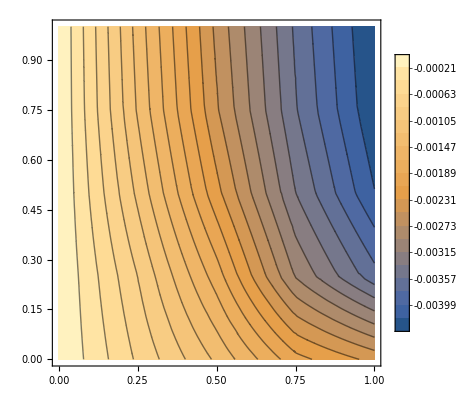

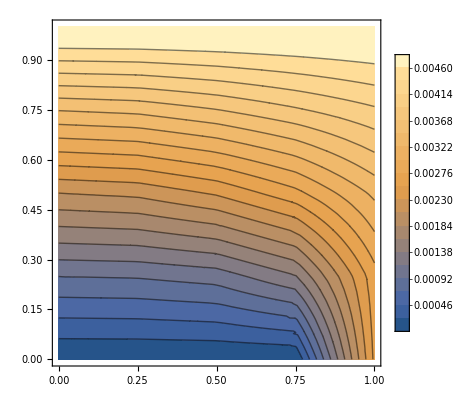

```mathematica
ContourPlot[Ufvec[[1]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[Ufvec[[2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 2D

```mathematica
ContourPlot[StressMatf[[1,1]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[1,2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[2,2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[3,3]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Plot Displacement 3D

```mathematica
SliceContourPlot3D[Ufvec[[1]]@@{x1,x2,x3},Automatic,{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 3D

```mathematica
SliceContourPlot3D[StressMatf[[1,1]]@@{x1,x2,x3},Automatic,{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```